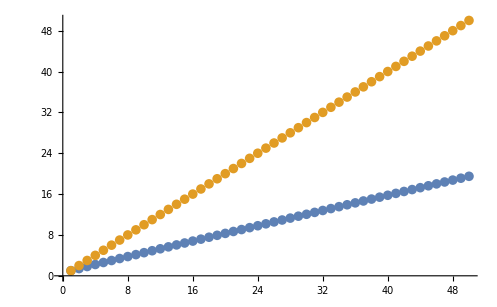

```mathematica
ListPlot[{Table[(n!)^(1/n),{n,50}],Table[n,{n,50}]}]
```

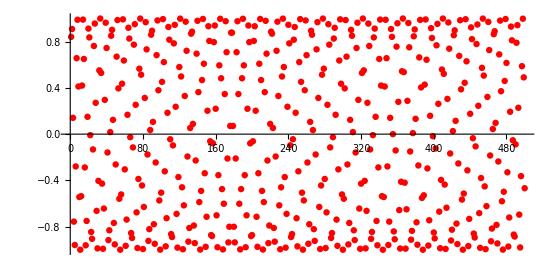

```mathematica
ListPlot[Table[Sin[n],{n,500}],AspectRatio->1/2,PlotStyle->Red]
```

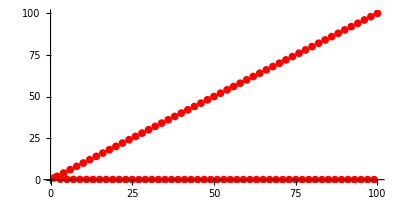

```mathematica
ListPlot[Table[n^((-1)^n),{n,100}],AspectRatio->1/2,PlotStyle->Red]
```

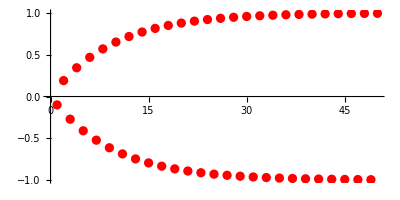

```mathematica
ListPlot[Table[(-1)^n-(-0.9)^n,{n,50}],AspectRatio->1/2,PlotStyle->Red]
```

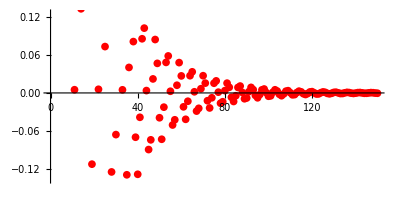

```mathematica
ListPlot[Table[(-0.95)^n*Sin[2n],{n,150}],AspectRatio->1/2,PlotStyle->Red]
```

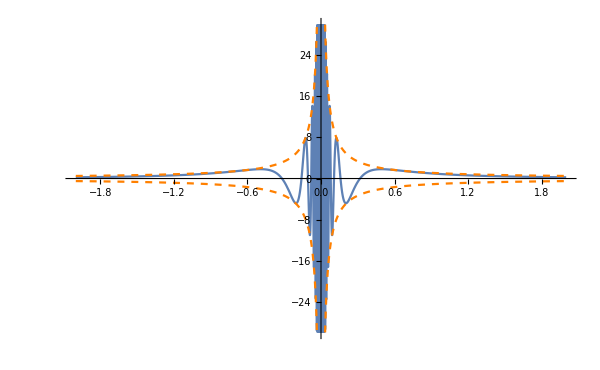

```mathematica
p1=Plot[Sin[1/x]/x,{x,-2,2},PlotRange->{-30,30},PlotPoints->100];
p2=Plot[{1/x,-1/x},{x,-2,2},PlotPoints->100,PlotStyle->{{Orange,Dashed},{Orange,Dashed}},Exclusions->{0},PlotRange->{-30,30}];
Show[p1,p2]
```

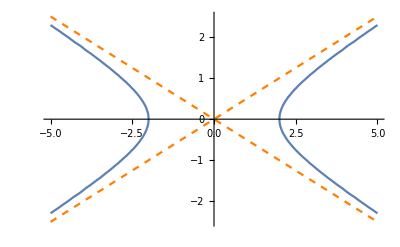

```mathematica
p1=Plot[x/2,{x,-5,5},PlotStyle->{Orange,Dashed}];
p2=Plot[-x/2,{x,-5,5},PlotStyle->{Orange,Dashed}];
p3=ContourPlot[x^2/4-y^2==1,{x,-5,5},{y,-5,5}];
Show[p1,p2,p3]
```

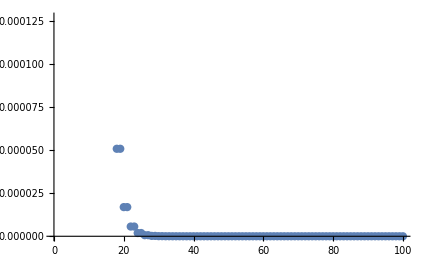

```mathematica
ListPlot[Table[1/(3^(Floor[n/2])),{n,1,100}]]
```

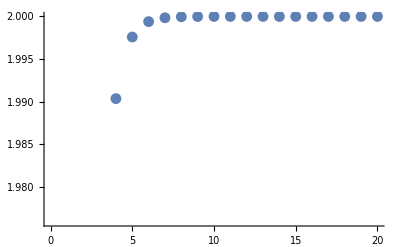

```mathematica
f[1]=Sqrt[2];
f[n_]:=Sqrt[2+f[n-1]];
xn=Table[f[n],{n,1,20}];
ListPlot[xn]
```

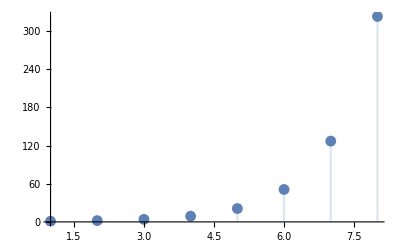

```mathematica
FindSequenceFunction[{1,2,4,9},n];
DiscretePlot[%,{n,1,8}]
```

```mathematica
RSolveValue[a[n+1]-2a[n]==1,a[n],n]
```

-1+2^n+2^(-1+n) C[1]

```mathematica
RSolveValue[{a[n+1]-2a[n]==1,a[0]==1},a[n],n]
```

-1+2^(1+n)

```mathematica
RecurrenceTable[{a[n]==a[n-1]+a[n-2],a[1]==1,a[2]==1},a,{n,10}]
```

{1,1,2,3,5,8,13,21,34,55}

```mathematica
RSolveValue[{a[n]==a[n-1]+a[n-2],a[1]==1,a[2]==1},a[n],n]
```

Fibonacci[n]

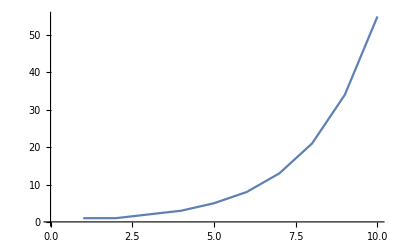

```mathematica
ListLinePlot[{1,1,2,3,5,8,13,21,34,55}]
```

{{0.142857,0.33},«2498»,{-0.0536288,-0.613564}}

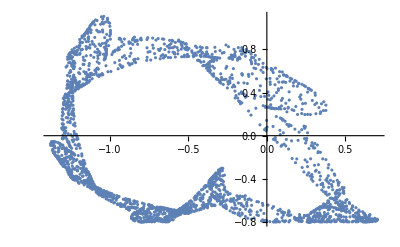

```mathematica
RecurrenceTable[{x[n+1]==0.7x[n]+y[n], 
    y[n+1]==-0.7989995+x[n]^2,x[1]==0.142857,y[1]==0.33},{x,y},{n,1,2500}]//Short
ListPlot[%]
```